```mathematica
<<UNET`
```

```mathematica
hearts  = FileNames["*.tiff", "C:\\Users\\Matteo\\Desktop\\hearts3d", Infinity];
labels  = FileNames["*.tiff", "C:\\Users\\Matteo\\Desktop\\labels3d", Infinity];
rawData = {Image3D /@ Import /@ hearts, Image3D /@ Import /@ labels} //Transpose;
```

```mathematica
trainingData=Map[ImageResize[#,{64,64,16},Resampling->"Nearest"]&,rawData //Flatten,2] ~ Partition ~2; 
{data,label}=trainingData//Transpose;
data={ImageData[#]}&/@ data;
label=Round[3*ImageData[#]+1]&/@label;
```

```mathematica
trainingData[[1;;10]]
```

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

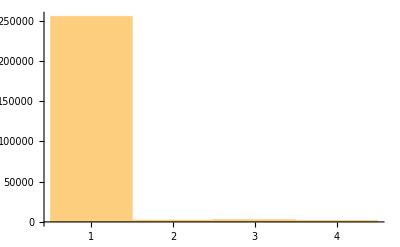

```mathematica
label[[10]] //Flatten// Histogram
```

```mathematica
{train,valid,testData,testLabel,order}=SplitTrainData[data,label];
```

Dimensions data: {170,1,16,64,64} - Dimensions label: {170,16,64,64}

Number of Samples in each set: {119,34,17}

```mathematica
(*train the net*)
before = Now;
{{net,trained,netTrained},{result,iou}}=TrainUNET[train,valid,{testData,testLabel},BatchSize->16,MaxTrainingRounds->700,NetParameters->32,TargetDevice->{"GPU", 1},LearningRate->.0001,(*COMMAND USED FOR SIZE 64*)
AugmentTrainData->{"90",True,True},BlockType->"ResNet"];
after = Now;
after - before
(*711 epochs*, 1h training*)
MakeNetPlots[trained] (*64*)
```

channels: 1 - classes: 4 - Dimensions :{16,64,64}

```mathematica
MakeNetPlots[trained] 
Export["netTrained64.wlnet", netTrained, "WLNet"]
```

netTrained64.wlnet

```mathematica
trained
```

```mathematica
before = Now;
{{net,trained,netTrained},{result,iou}}=TrainUNET[train,valid,{testData,testLabel},BatchSize->4,MaxTrainingRounds->5000,NetParameters->32,TargetDevice->{"GPU", 1},LearningRate->.00005,(*COMMAND USED FOR SIZE 96*)
AugmentTrainData->{"90",True,True},BlockType->"ResNet"];
after = Now;
after - before
Export["netTrained96.wlnet", netTrained, "WLNet"] (*455 epochs*)
```

channels: 1 - classes: 4 - Dimensions :{16,96,96}

Evaluating test data

DICE per class: {1→0.84,2→0.84,3→0.84,4→0.84}

1.5794 h

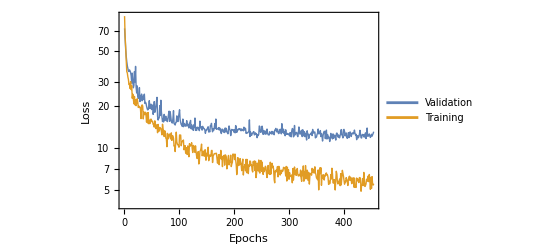
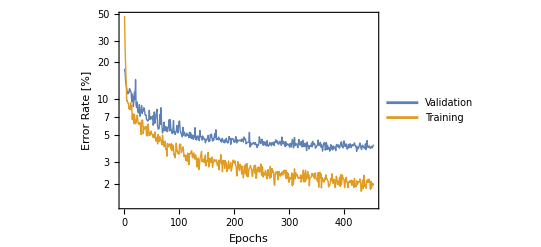

```mathematica
MakeNetPlots[trained] (*96*)
```

```mathematica
compare[x_] := {img = Image3D[testData[[x,  1]]], res = netTrained[{ImageData@img}] [[;;, ;;, ;;, 2;;4]] //Image3D, img+res}
```

```mathematica
compare[4]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
-Graphics3D-+Image3D[testData[[5,  1]]]~ImageResize~{64,64,16}
```

-Graphics3D-

```mathematica
data //Dimensions
```

{164,1,128,128}

```mathematica
Image /@ (netTrained/@ data)[[;;, ;;,;;,2;;4]]
```